10

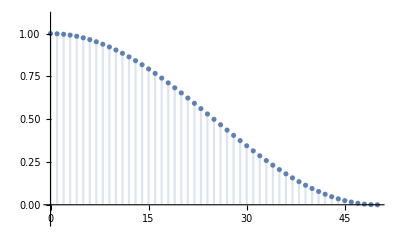

```mathematica
M = 100;
α=10
Dk[k_, M_, α_]:=Sum[Cos[2 Pi k / M r]/r^α, {r, 1, M/2}];
DiscretePlot[(Dk[k, M, α] - Dk[M/2, M, α])/(Dk[0, M, α] - Dk[M/2, M, α]), {k, 0, M/2}, PlotRange->{-0.1, 1.1}]
```

```mathematica
k = 0;
(Dk[k, M] - Dk[M/2, M])/(Dk[0, M] - Dk[M/2, M])
```

1

```mathematica
Dkmean[M_, α_] :=2 Sum[(Dk[k, M, α] - Dk[M/2, M, α])/(Dk[0, M, α] - Dk[M/2, M, α]), {k, 0, M/2}]/ M;
```

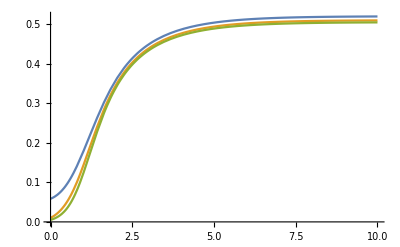

```mathematica
Plot[{Dkmean[50, α] , Dkmean[100, α], Dkmean[200, α]  },{α, 0, 10}]
```